...........................................................a[n]已经算完

...........................................................计算5到n个的部分和

...........................................................5到n个部分和的图像

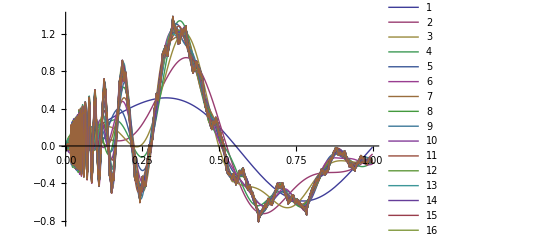

...........................................................cauchy判别

...........................................................cauchy判别图像

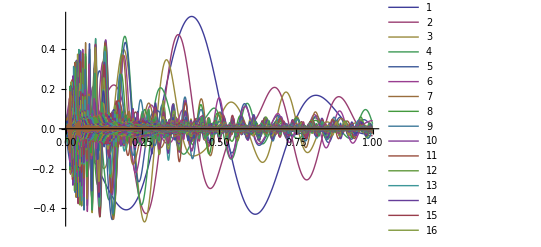

...........................................................截断的最大值

...........................................................截断的最大值列表

(0.564295 | {x→0.410501}
0.472785 | {x→0.366519}
0.346667 | {x→0.328551}
0.464453 | {x→0.192795}
0.434167 | {x→0.194513}
0.367547 | {x→0.189834}
0.370393 | {x→0.185999}
0.440377 | {x→0.129652}
0.416301 | {x→0.13012}
0.446802 | {x→0.130438}
0.226236 | {x→0.0924986}
0.306315 | {x→0.0942926}
0.389004 | {x→0.1276}
0.382041 | {x→0.0966666}
0.394736 | {x→0.0970521}
0.406564 | {x→0.0971544}
0.453294 | {x→0.0976868}
0.421234 | {x→0.0970486}
0.425132 | {x→0.0973016}
0.409304 | {x→0.0968904}
0.400632 | {x→0.0779508}
0.428283 | {x→0.0776788}
0.151562 | {x→0.0933955}
0.432925 | {x→0.0649431}
0.377498 | {x→0.0645996}
0.377364 | {x→0.0556102}
0.399363 | {x→0.0555766}
0.380515 | {x→0.0553989}
0.348308 | {x→0.0486298}
0.392634 | {x→0.0486611}
0.389304 | {x→0.0485614}
0.339873 | {x→0.0484851}
0.368954 | {x→0.043256}
0.405176 | {x→0.0432512}
0.0864476 | {x→0.0540648}
0.33055 | {x→0.0431058}
0.374814 | {x→0.0389059}
0.0985546 | {x→0.0479065}
0.354194 | {x→0.0353789}
0.346351 | {x→0.0353461}
0.316589 | {x→0.032458}
0.363999 | {x→0.0324285}
0.215924 | {x→0.0355145}
0.306039 | {x→0.0299533}
0.219248 | {x→0.0325299}
0.0609645 | {x→0.081942}
0.184011 | {x→0.0244108}
0.0510108 | {x→0.0801291}
0.22152 | {x→0.0243949}
0.235848 | {x→0.0217085}
0.190236 | {x→0.018603}
0.0974946 | {x→0.0156356}
0.0421742 | {x→0.0534512}
0.0990415 | {x→0.0204873}
0.207847 | {x→0.0150495}
0.0452278 | {x→0.0526743}
0.0443178 | {x→0.0503992}
0.204639 | {x→0.0156285}
0.0376275 | {x→0.0476888}
0.209798 | {x→0.013038}
0.162565 | {x→0.0130307}
0.19409 | {x→0.0139669})

...........................................................截断的最大值图像

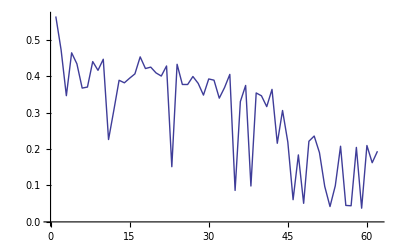

...........................................................LHS

...........................................................RHS

...........................................................LHS/RHS

{2.27636,4.39395,4.72163,4.75134,6.06783,7.16556,6.79869,9.26468,8.69964,8.20038,8.95778,11.2402,10.5044,11.264,10.5264,11.1855,10.4647,11.042,13.1293,12.293,15.1237,14.792,17.1391,16.4734,18.4904,18.9935,20.832,21.1588,22.8426,23.0371,23.166,24.6806,24.7248,24.7271,27.5432,27.4461,27.1778,29.6604,29.183,31.4705,33.6963,32.9759,35.0431,37.0538,37.5828,39.4984,41.2228,47.8375,49.4878,53.5053,55.6655,61.7916,61.8599,65.9889,69.8901,72.1523,74.2306,76.146,77.9164,82.4344,82.4967,83.8997}

...........................................................LHS/RHS的图像

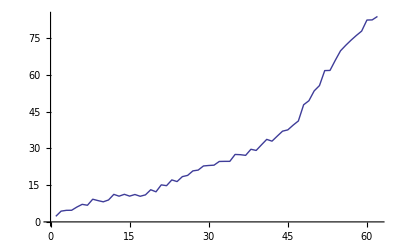

```mathematica
a[n_]:=(-1)^Floor[√n] 1/n;
Print["...........................................................a[n]已经算完"];
lst={10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200,250,300,350,400,450,500,550,600,650,700,750,800,850,900,950,1000,1100,1200,1300,1400,1500,1600,1700,1800,1900,2000,2500,3000,3500,4000,4500,5000,5500,6000,6500,7000,7500,8000,8500,9000,9500,10000};
Print["...........................................................计算5到n个的部分和"];
tbl=Table[∑_(k=5)^lst[[n]] (a[k]Sin[k x]),{n,Length[lst]}];
Print["...........................................................5到n个部分和的图像"];
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
Print["...........................................................cauchy判别"];
tbl=Table[∑_(k=lst[[n]])^(2 lst[[n]]) (a[k]Sin[k x]),{n,1,Length[lst]}];
Print["...........................................................cauchy判别图像"];
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
Print["...........................................................截断的最大值"];
cnvrgnclst=Table[NMaximize[{∑_(k=lst[[n]])^(2 lst[[n]]) (a[k]Sin[k x]),0<x<1},x],{n,1,Length[lst]}];
Print["...........................................................截断的最大值列表"];
cnvrgnclst//MatrixForm
Print["...........................................................截断的最大值图像"];
ListLinePlot[Map[First,cnvrgnclst]]
Print["...........................................................LHS"];
diff=Table[N[Total[Abs[Differences[Table[a[k],{k,lst[[m]],2 lst[[m]]}]]]]],{m,1,Length[lst]}];
Print["...........................................................RHS"];
abs=Table[N[1/lst[[m]] Total[Table[Abs[a[k]],{k,lst[[m]],2 lst[[m]]}]]],{m,1,Length[lst]}];
Print["...........................................................LHS/RHS"];
diff/abs
Print["...........................................................LHS/RHS的图像"];
ListLinePlot[diff/abs]
```

...........................................................LHS

...........................................................RHS

...........................................................LHS/RHS

{2.27636,0.684179,2.73374,3.44303,0.706043,2.3281,2.60463,2.88074,3.15655,3.43217,0.714316,0.714897,2.14617,2.25756,2.3689,2.48019,2.59145,2.70267,2.81387,2.92505,3.48069,0.718754,2.33254,2.56402,2.79543,3.02681,3.25815,3.48947,0.720149,0.720234,2.19837,2.29711,2.39585,2.49458,2.59331,2.69203,2.88946,3.08687,3.28428,3.48168,0.720828,0.72086,2.18244,2.26849,2.35454,2.44059,2.87081,3.30101,0.721125,2.24559,2.43621,2.62684,2.81746,3.00807,3.19869,3.3893,3.57992,0.72125,2.17825,2.26397,2.34969,2.43541}

...........................................................LHS/RHS的图像

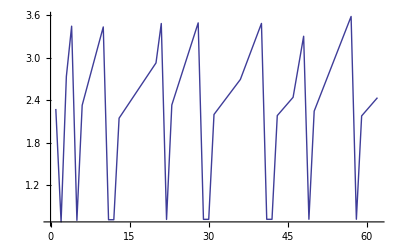

```mathematica
a[n_]:=(-1)^Floor[Log[n]Log[Log[Log[n]]]] 1/n;
lst={10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200,250,300,350,400,450,500,550,600,650,700,750,800,850,900,950,1000,1100,1200,1300,1400,1500,1600,1700,1800,1900,2000,2500,3000,3500,4000,4500,5000,5500,6000,6500,7000,7500,8000,8500,9000,9500,10000};
Print["...........................................................LHS"];
diff=Table[N[Total[Abs[Differences[Table[a[k],{k,lst[[m]],2 lst[[m]]}]]]]],{m,1,Length[lst]}];
Print["...........................................................RHS"];
abs=Table[N[1/lst[[m]] Total[Table[Abs[a[k]],{k,lst[[m]],2 lst[[m]]}]]],{m,1,Length[lst]}];
Print["...........................................................LHS/RHS"];
diff/abs
Print["...........................................................LHS/RHS的图像"];
ListLinePlot[diff/abs]
```

...........................................................LHS

...........................................................RHS

...........................................................LHS/RHS

...........................................................LHS/RHS的图像

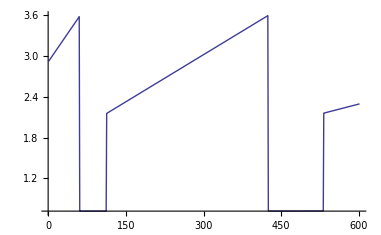

```mathematica
up=800;
Print["...........................................................LHS"];
diff=Table[N[Total[Abs[Differences[Table[a[k],{k,m,2 m}]]]]],{m,200,up}];
Print["...........................................................RHS"];
abs=Table[N[1/m Total[Table[Abs[a[k]],{k,m,2 m}]]],{m,200,up}];
Print["...........................................................LHS/RHS"];
da=diff/abs;
Print["...........................................................LHS/RHS的图像"];
ListLinePlot[da]
```

```mathematica
Length[da]
```

495

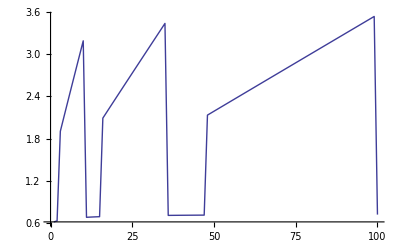

```mathematica
da=diff/abs;
ListLinePlot[da[[1;;100]]]
```

```mathematica
plotimage[n_]:=Module[{m=n},
Print[Plot[∑_(k=lst[[n]])^(2 lst[[n]]) (a[k]Sin[k x]),{x,0,1},PlotRange->Full,PlotLegends->Automatic]];
m]
```

```mathematica
a[n_]:=(-1)^Floor[√n] 1/n;
```

...........................................................cauchy判别

...........................................................cauchy判别图像

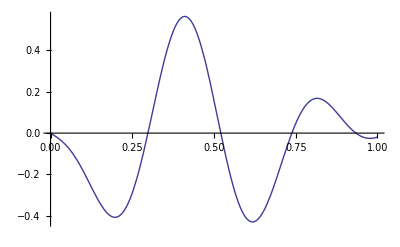

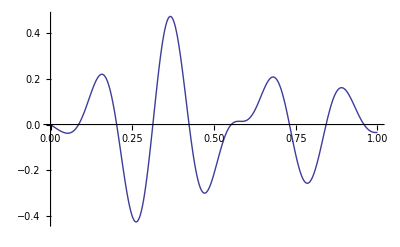

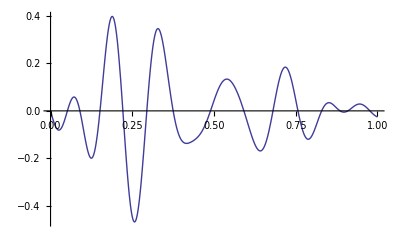

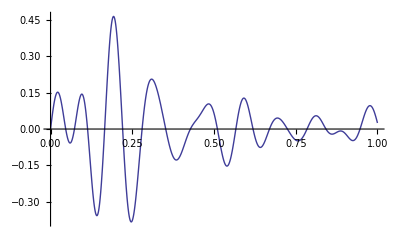

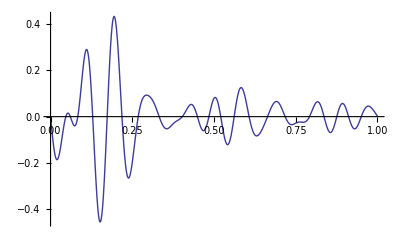

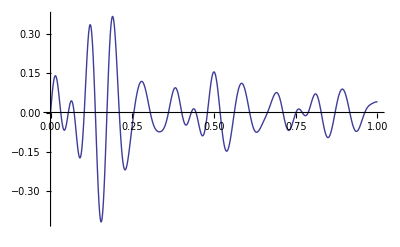

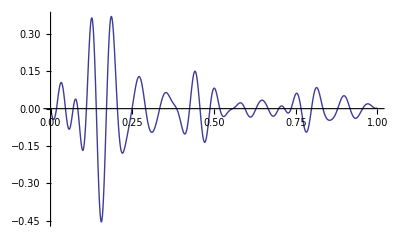

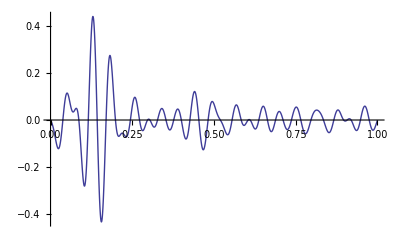

$Aborted

...........................................................截断的最大值

$Aborted

...........................................................截断的最大值列表

cnvrgnclst

...........................................................截断的最大值图像

ListLinePlot::lpn: cnvrgnclst is not a list of numbers or pairs of numbers.

ListLinePlot[cnvrgnclst]

```mathematica
Print["...........................................................cauchy判别"];
n=1;
Print["...........................................................cauchy判别图像"];
While[n≤Length[lst],plotimage[n];n++]
Print["...........................................................截断的最大值"];
cnvrgnclst=Table[NMaximize[{∑_(k=lst[[n]])^(2 lst[[n]]) (a[k]Sin[k x]),0<x<1},x],{n,1,Length[lst]}];
Print["...........................................................截断的最大值列表"];
cnvrgnclst//MatrixForm
Print["...........................................................截断的最大值图像"];
ListLinePlot[Map[First,cnvrgnclst]]
```

```mathematica
∑_(n=1)^∞ ((-1)^n Sin[2n x]/(2n))
```

-1/4 ⅈ (-Log[1+ⅇ^(2 ⅈ x)]+Log[ⅇ^(-2 ⅈ x) (1+ⅇ^(2 ⅈ x))])

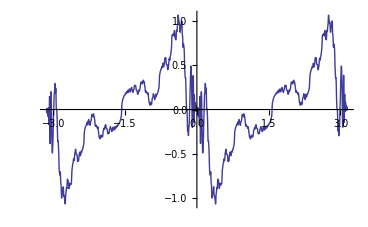

```mathematica
Plot[∑_(n=1)^200 ((-1)^Floor[√n] Sin[2n x]/(2n)),{x,-π,π}]
```

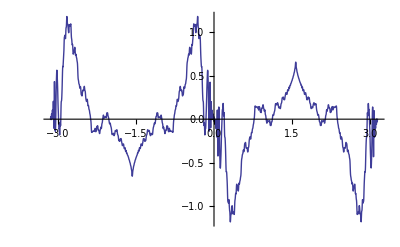

```mathematica
Plot[∑_(n=1)^200 ((-1)^Floor[√n] Sin[(2n+1) x]/(2n)),{x,-π,π}]
```

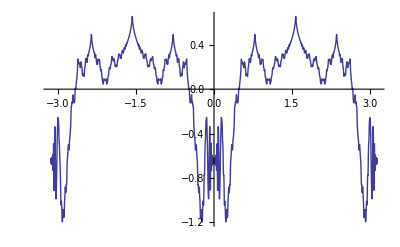

```mathematica
Plot[∑_(n=1)^200 ((-1)^Floor[√n] Cos[(2n) x]/(2n)),{x,-π,π}]
```

```mathematica
N[∑_(n=200)^400 ((-1)^Floor[√n] 1/(2n))]
```

0.00187718

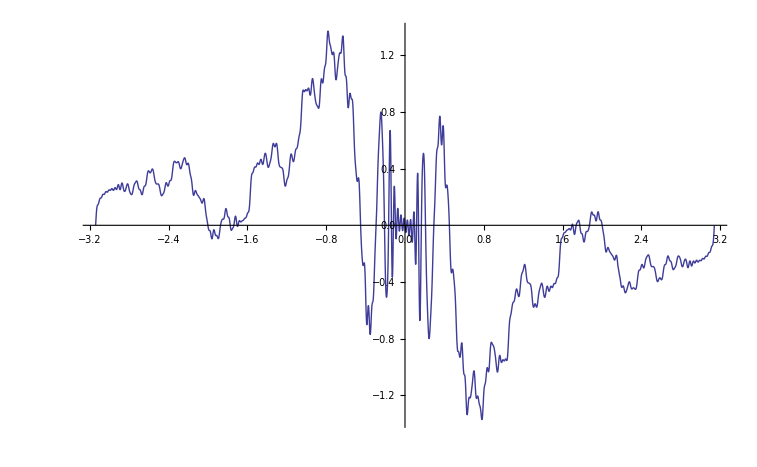

```mathematica
Plot[∑_(n=1)^200 ((-1)^Floor[√n] Sin[n x]/(2Floor[(n+2)/2])),{x,-π,π}]
```

...........................................................a[n]已经算完

...........................................................计算5到n个的部分和

...........................................................5到n个部分和的图像

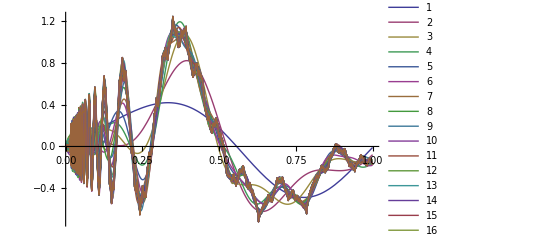

...........................................................cauchy判别

...........................................................cauchy判别图像

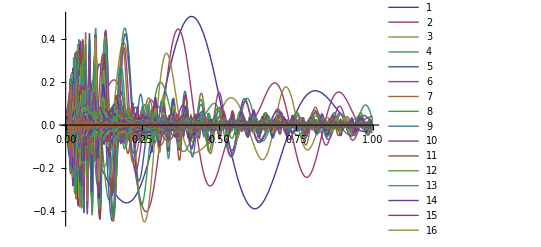

...........................................................截断的最大值

...........................................................截断的最大值列表

(0.506111 | {x→0.410177}
0.447104 | {x→0.366447}
0.334473 | {x→0.328396}
0.451941 | {x→0.192801}
0.424736 | {x→0.194484}
0.360942 | {x→0.189813}
0.364542 | {x→0.185979}
0.434604 | {x→0.129658}
0.411404 | {x→0.130126}
0.441916 | {x→0.130436}
0.224481 | {x→0.0925095}
0.303674 | {x→0.0943019}
0.385686 | {x→0.127596}
0.379222 | {x→0.09667}
0.391941 | {x→0.0970553}
0.403923 | {x→0.0971557}
0.450392 | {x→0.0976872}
0.418692 | {x→0.0970484}
0.422745 | {x→0.0973011}
0.40703 | {x→0.096889}
0.398945 | {x→0.0779515}
0.426727 | {x→0.0776785}
0.151013 | {x→0.0933955}
0.431744 | {x→0.0649431}
0.376554 | {x→0.0645993}
0.376587 | {x→0.0556104}
0.398581 | {x→0.0555767}
0.379817 | {x→0.0553988}
0.347762 | {x→0.0486299}
0.392042 | {x→0.0486611}
0.388736 | {x→0.0485613}
0.339386 | {x→0.048485}
0.368501 | {x→0.0432561}
0.404689 | {x→0.0432512}
0.0863234 | {x→0.0540643}
0.330176 | {x→0.0431057}
0.374448 | {x→0.0389059}
0.0984364 | {x→0.0479065}
0.353907 | {x→0.035379}
0.346077 | {x→0.035346}
0.31638 | {x→0.032458}
0.363755 | {x→0.0324285}
0.215762 | {x→0.0355145}
0.305868 | {x→0.0299533}
0.219099 | {x→0.0325299}
0.060935 | {x→0.081942}
0.183957 | {x→0.0244108}
0.050988 | {x→0.0801291}
0.221441 | {x→0.0243949}
0.235775 | {x→0.0217085}
0.190201 | {x→0.018603}
0.189215 | {x→0.0177528}
0.0421661 | {x→0.0534512}
0.0990195 | {x→0.0204873}
0.207817 | {x→0.0150495}
0.0452191 | {x→0.0526743}
0.0443099 | {x→0.0503992}
0.204607 | {x→0.0156285}
0.0376215 | {x→0.0476888}
0.209776 | {x→0.013038}
0.162548 | {x→0.0130307}
0.194065 | {x→0.0139669})

...........................................................截断的最大值图像

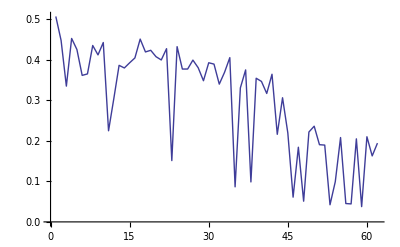

...........................................................LHS

...........................................................RHS

...........................................................LHS/RHS

{2.15587,4.36627,4.66537,4.72829,6.04053,7.11896,6.79078,9.24673,8.67901,8.19642,8.94786,11.2311,10.4889,11.2427,10.5242,11.1795,10.454,11.0279,13.1162,12.2907,15.1122,14.7844,17.1353,16.4719,18.4859,18.992,20.8282,21.1566,22.8388,23.0359,23.1624,24.6795,24.7226,24.7262,27.5417,27.4431,27.1754,29.6589,29.1821,31.4683,33.6951,32.9753,35.0416,37.0531,37.5812,39.4977,41.2223,47.8369,49.4871,53.5047,55.6648,61.7912,61.8595,65.9884,69.8898,72.1518,74.2303,76.1455,77.9162,82.4341,82.4963,83.8996}

...........................................................LHS/RHS的图像

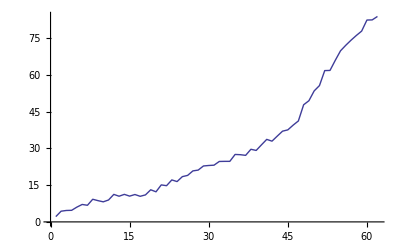

```mathematica
a[n_]:=(-1)^Floor[√n] 1/(2Floor[(n+2)/2]);
Print["...........................................................a[n]已经算完"];
lst={10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200,250,300,350,400,450,500,550,600,650,700,750,800,850,900,950,1000,1100,1200,1300,1400,1500,1600,1700,1800,1900,2000,2500,3000,3500,4000,4500,5000,5500,6000,6500,7000,7500,8000,8500,9000,9500,10000};
Print["...........................................................计算5到n个的部分和"];
tbl=Table[∑_(k=5)^lst[[n]] (a[k]Sin[k x]),{n,Length[lst]}];
Print["...........................................................5到n个部分和的图像"];
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
Print["...........................................................cauchy判别"];
tbl=Table[∑_(k=lst[[n]])^(2 lst[[n]]) (a[k]Sin[k x]),{n,1,Length[lst]}];
Print["...........................................................cauchy判别图像"];
Show[Plot[tbl,{x,0,1},PlotRange->Full,PlotLegends->Automatic]]
Print["...........................................................截断的最大值"];
cnvrgnclst=Table[NMaximize[{∑_(k=lst[[n]])^(2 lst[[n]]) (a[k]Sin[k x]),0<x<1},x],{n,1,Length[lst]}];
Print["...........................................................截断的最大值列表"];
cnvrgnclst//MatrixForm
Print["...........................................................截断的最大值图像"];
ListLinePlot[Map[First,cnvrgnclst]]
Print["...........................................................LHS"];
diff=Table[N[Total[Abs[Differences[Table[a[k],{k,lst[[m]],2 lst[[m]]}]]]]],{m,1,Length[lst]}];
Print["...........................................................RHS"];
abs=Table[N[1/lst[[m]] Total[Table[Abs[a[k]],{k,lst[[m]],2 lst[[m]]}]]],{m,1,Length[lst]}];
Print["...........................................................LHS/RHS"];
diff/abs
Print["...........................................................LHS/RHS的图像"];
ListLinePlot[diff/abs]
```

```mathematica
Table[a[k],{k,50,100}]
```

{-1/52,-1/52,-1/54,-1/54,-1/56,-1/56,-1/58,-1/58,-1/60,-1/60,-1/62,-1/62,-1/64,-1/64,1/66,1/66,1/68,1/68,1/70,1/70,1/72,1/72,1/74,1/74,1/76,1/76,1/78,1/78,1/80,1/80,1/82,-1/82,-1/84,-1/84,-1/86,-1/86,-1/88,-1/88,-1/90,-1/90,-1/92,-1/92,-1/94,-1/94,-1/96,-1/96,-1/98,-1/98,-1/100,-1/100,1/102}